```mathematica
WA = 5.40221; WB = 1838.675; WC = -31.737;
MA = 5.20409; MB = 1581.341; MC = -33.50;
P = 1;
TW = ((WB/(-Log[10,P]+WA))-WC);
TM = ((MB/(-Log[10,P]+MA))-MC);
```

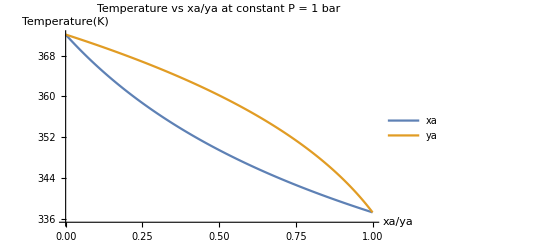

```mathematica
temp = Table[T,{T,TM,TW,((TW-TM)/100)}];
PAs[T_] = 10^(MA-(MB/(MC+T)));
PBs[T_] = 10^(WA-(WB/(WC+T)));
xa[T_] = (P-PBs[T])/(PAs[T]-PBs[T]);
ya [T_] = ((PAs[T]*PBs[T])/(P*(PBs[T]-PAs[T])))-(PAs[T]/(PBs[T]-PAs[T]));
xalist =xa[temp]; yalist = ya[temp];
xaplot = Transpose@{xalist,temp}; yaplot = Transpose@{yalist,temp};
plot1 =ListLinePlot[{xaplot,yaplot},PlotLegends -> {"xa","ya"},AxesLabel -> {"xa/ya","Temperature(K)"}, PlotLabel -> "Temperature vs xa/ya at constant P = 1 bar"]
```

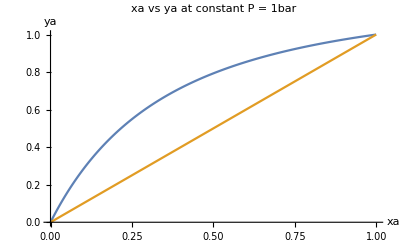

```mathematica
xayaplot = Transpose@{xalist,yalist}; x = {0,1}; y = {0,1}; xy = Transpose@{x,y};
plot2 = ListLinePlot[{xayaplot,xy},AxesLabel -> {"xa","ya"}, PlotLabel -> "xa vs ya at constant P = 1bar"]
```